```mathematica
c=299792458.;
ℏ=1.0545718*10^-34;
f770=3.892596*10^14;
f680=c/(680*10^-9);
f578=c/(578*10^-9);
f532=c/(632.*10^-9);
Γ399=2*π*30.*10^6;
Γ556=2*π*180.*10^3;
Γ770=3.7*10^7;
Γ680=2.7*10^7;
Γ578=2π*6.*10^-3;
Isat399=600;
Isat556=1.39;
Isat578=(ℏ(2π*f578)^3)/(4π c^2)Γ578
Isat770=(ℏ(2π*f770)^3)/(4π c^2)Γ770
Isat680=(ℏ(2π*f680)^3)/(4π c^2)Γ680
```

1.21836×10^-7

50.5457

53.5875

```mathematica
π ((2.5*11)/(350./26))^2
```

13.1107

```mathematica
0.01*13*10^-12*10*Isat556/(6.626*10^-34*c/(556.*10^-9))
```

5.05779×10^6

### scattering rate

```mathematica
ρee=1/2 s/(1+((2Δ)/Γ)^2+s);
Rsc=Γ ρee;
```

```mathematica
Ω0=Ω/.{Γ->Γ556,s-> 11000.,Δ->0}
```

8.38752×10^7

```mathematica
Rsc2=Γ Ωb^2/(4 Δ^2);
```

```mathematica
Rsc2/.{Γ->Γ556,Ωb->8.38752288646445*^7,Δ->2π 160.*10^6}
```

1968.16

```mathematica
Rsc/.{s->0.000106,Δ->2π*0.0,Γ->Γ399}
```

9989.21

```mathematica
Rsc/.{s->11000.,Δ->2π*160.0*10^6,Γ->Γ556}
```

1961.33

```mathematica
Rsc/.{s->0.006,Δ->2π*0.0*10^6,Γ->Γ399}
```

562114.

```mathematica
Rsc/.{s->1.3*10^10,Δ->2π*c/((551.5*10^-9)^2)(555.8-551.5)*10^-9,Γ->Γ556}
```

3.31476

```mathematica
Δ1S3=f532-f680
```

3.34839×10^13

```mathematica
Rsc/.{s->1.97*10^6,Δ->2π*Δ1S3,Γ->Γ770}
```

0.281806

### intensity / saturation

```mathematica
Clear[I0]
```

```mathematica
Isat399=600;
Isat556=1.39;
I0=(2*P0)/(π w0^2);
```

```mathematica
(I0/.{P0->200.*10^-9,w0->0.001})/Isat399
```

0.000212207

```mathematica
(I0/.{P0->6.*10^-3,w0->460.*10^-9})/Isat770
```

1.9708×10^6

```mathematica
s=2(Ω/Γ)^2;
```

```mathematica
Ωr=Ω^2/(4Δ);
```

```mathematica
Rsc2=Γ Ω^2/(4 Δ^2);
```

```mathematica
Rscraman=2*Γ556*(2π*1.3*10^5)/(2π 380.*10^6)
```

773.824

```mathematica
1/Rscraman
```

0.00129228

```mathematica
Ωr/Rsc2
```

Δ/Γ

```mathematica
(380.*10^6)/(180.*10^3)
```

2111.11

```mathematica
Cos[π*1.03]
```

-0.995562

```mathematica
Ωr0=2π 1.*10^6;
τrabi=2(√2)/(Ωr0*0.02);
t0=(2π)/Ωr0;
t0/τrabi
E^(-t0/τrabi)
```

0.0444288

0.956544

```mathematica
zr=(π w0^2)/λ;
zr/.{w0->0.11*10^-3,λ->556.*10^-9}
```

0.0683692

```mathematica
1-E^(-10/317.)
```

0.0310534

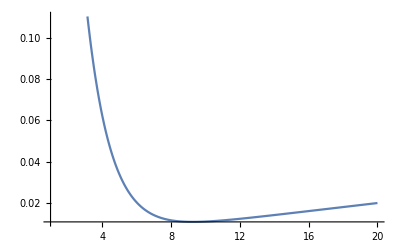

```mathematica
Plot[E^(-t/1.41)+(1-E^(-t/1000)),{t,1,20}]
```

```mathematica
E^(-7.5/1.08)
```

0.000963976

```mathematica
1 - E^(-7.5/949.01128)
```

0.00787182

```mathematica
0.003690032705558899
```

0.00369003

```mathematica
tau2=0.61677;
tau1=1082;
```

```mathematica
Plot[{Exp[-t/tau1],1-Exp[-t/tau2]},{t,0,10}]
```

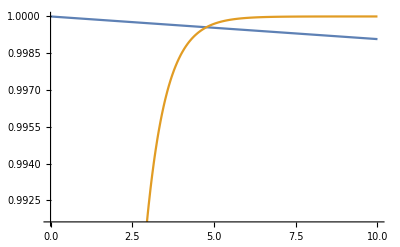

-Graphics-

```mathematica
Nrabi=(√2)/(π 0.02)
```

22.5079

```mathematica
1/(√(200*50.))
```

0.01

```mathematica
200*92/3600.
```

5.11111